```mathematica
SetDirectory["/home/lindorfer/ReWiTech/Masterarbeit/Programs/Simplified_B/Data/"]
```

/home/lindorfer/ReWiTech/Masterarbeit/Daten

```mathematica
coords=Import["TravelTim1_test.dat"]
```

{{12602,5915},{11746,11976},{13674,2963},{5028,11523},{4166,8309},{7160,9433},{5471,7701},{14283,13742},{9535,10759},{2124,9104},{244,3643},{2058,12062},{2350,6014},{1946,1632},{14983,3273},{7693,12586},{9189,4440},{9563,7864},{7403,14591},{4387,11570},{7901,11548},{6003,13372},{4249,5286},{12115,13785},{1046,14239},{7889,1290},{2883,9948},{13353,5233},{962,300},{6865,946},{3574,14559},{13533,12763},{3999,8096},{5628,11403},{7688,10015},{7974,589},{6564,13977},{13962,10814},{4264,11078},{9599,5310},{10317,2489},{6601,13201},{12438,4955},{3434,13400},{5255,10300},{14347,8829},{9859,12880},{6593,13859}}

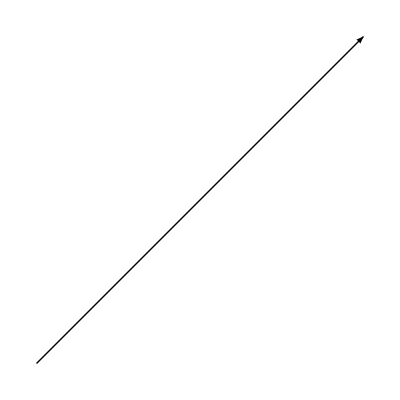

```mathematica
arrow=Graphics[Arrow[{{0,0},{5000,5000}}]]
```

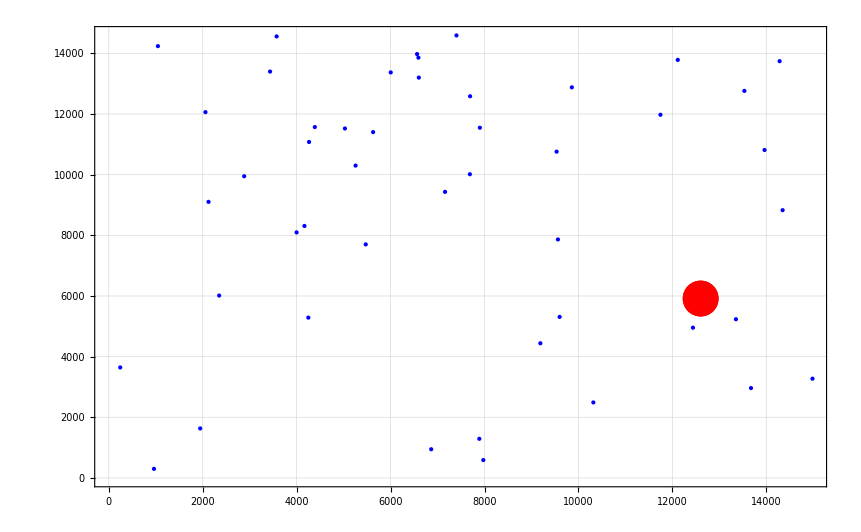

```mathematica
graph=ListPlot[{coords,{{12602,5915}}},
Frame->True,
LabelStyle->25,
PlotStyle->{{PointSize[Large],Blue},{PointSize[0.03],Red}},
PlotTheme->{"Classic","Detailed"}]
```

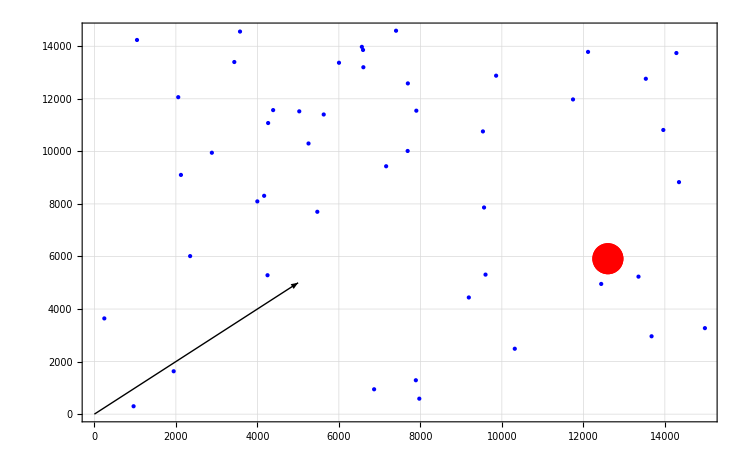

```mathematica
Show[graph,arrow]
```

## Initial Solution for capacity = 30

```mathematica
path={1,25,12,44,1,29,14,11,1,11,13,23,1,31,44,1,44,20,39,4,1,10,27,5,1,19,37,48,1,48,1,48,42,22,16,1,4,34,45,1,33,5,1,5,7,1,45,6,1,23,7,6,1,16,21,35,6,1,8,32,24,2,1,30,26,36,41,17,40,1,47,2,1,6,9,2,38,46,1,18,40,43,28,3,1,15,3,46,1,46,1};
```

```mathematica
arrowlist={Arrowheads[0.015]};
For[i = 1, i ≤ Length[path]-1,i++,
If[path[[i]] == 1,
AppendTo[arrowlist,RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]],];
AppendTo[arrowlist,Arrow[{coords[[path[[i]]]],coords[[path[[i+1]]]]}]];
]
```

```mathematica
For[i = 1, i ≤ Length[path]-1,i++,
AppendTo[arrowlist,Arrow[{coords[[path[[i]]]],coords[[path[[i+1]]]]}]]
]
```

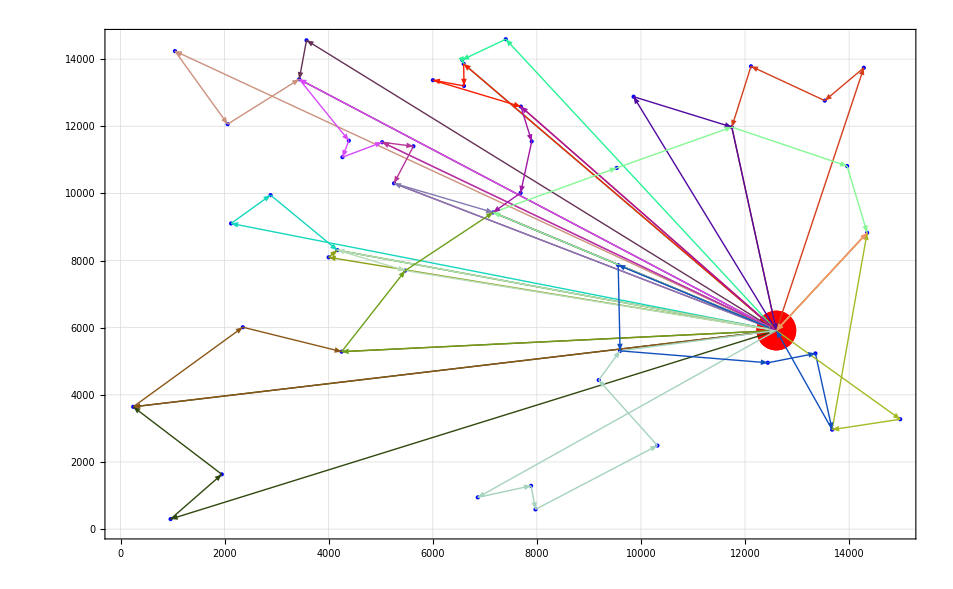

```mathematica
Show[graph,Graphics[arrowlist]]
```

## Initial Solution for capacity = 100

```mathematica
path={1,25,12,44,31,22,42,48,1,29,14,11,13,23,7,5,1,10,27,39,20,4,34,45,6,1,19,37,48,16,21,35,6,1,33,5,18,40,17,41,26,36,30,43,28,1,8,32,24,2,47,9,38,46,28,1,15,3,28,1}
```

{1,25,12,44,31,22,42,48,1,29,14,11,13,23,7,5,1,10,27,39,20,4,34,45,6,1,19,37,48,16,21,35,6,1,33,5,18,40,17,41,26,36,30,43,28,1,8,32,24,2,47,9,38,46,28,1,15,3,28,1}

```mathematica
arrowlist={Arrowheads[0.015]};
For[i = 1, i ≤ Length[path]-1,i++,
If[path[[i]] == 1,
AppendTo[arrowlist,RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]],];
AppendTo[arrowlist,Arrow[{coords[[path[[i]]]],coords[[path[[i+1]]]]}]];
]
```

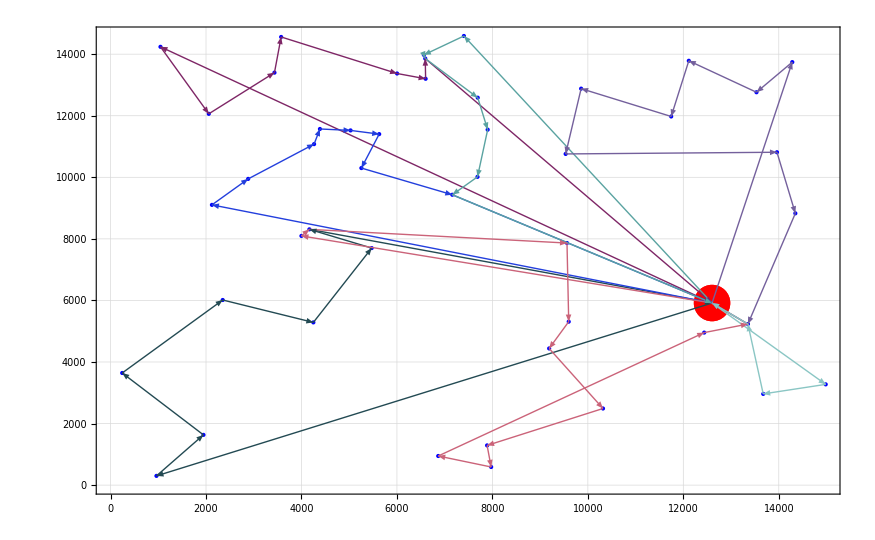

```mathematica
init=Show[graph,Graphics[arrowlist]]
```

## 2-opt for route 1 mit capacity = 100

```mathematica
path1={1,25,12,44,31,22,42,48,1};
path2={1,25,12,44,31,22,48,42,1};
```

```mathematica
arrowlist1={Arrowheads[0.015]};
For[i = 1, i ≤ Length[path1]-1,i++,
If[path1[[i]] == 1,
AppendTo[arrowlist1,RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]],];
AppendTo[arrowlist1,Arrow[{coords[[path1[[i]]]],coords[[path1[[i+1]]]]}]];
]
```

```mathematica
arrowlist2={Arrowheads[0.015]};
For[i = 1, i ≤ Length[path2]-1,i++,
If[path2[[i]] == 1,
AppendTo[arrowlist2,RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]],];
AppendTo[arrowlist2,Arrow[{coords[[path2[[i]]]],coords[[path2[[i+1]]]]}]];
]
```

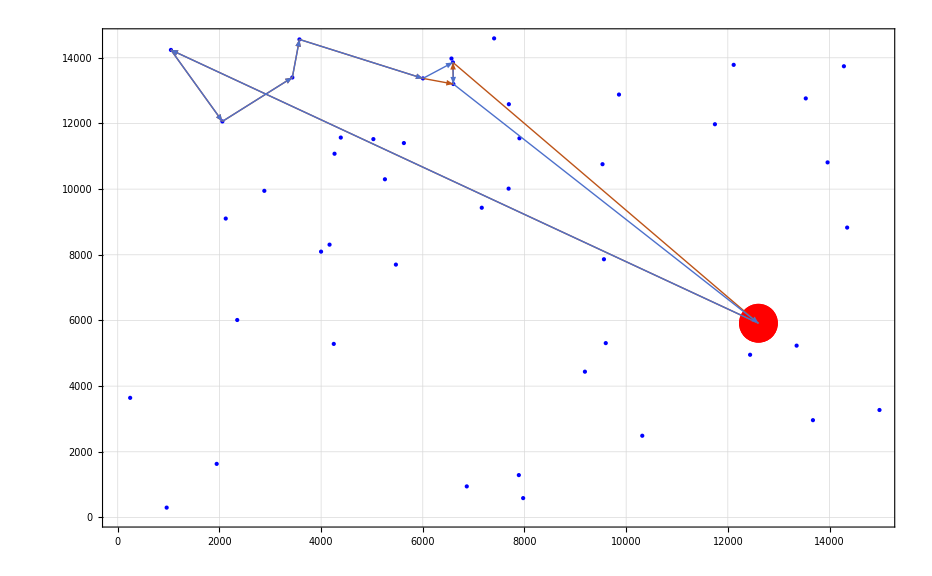

```mathematica
Show[graph,Graphics[arrowlist1],Graphics[arrowlist2]]
```

## 2-opt for route all routes mit capacity = 100

```mathematica
path ={1,12,25,31,44,22,48,42,1,14,29,11,13,23,5,7,1,10,27,39,20,4,34,45,6,1,19,37,48,16,21,35,6,1,43,17,40,18,5,33,30,36,26,41,28,1,9,47,2,24,8,32,38,46,28,1,15,3,28,1}
```

{1,12,25,31,44,22,48,42,1,14,29,11,13,23,5,7,1,10,27,39,20,4,34,45,6,1,19,37,48,16,21,35,6,1,43,17,40,18,5,33,30,36,26,41,28,1,9,47,2,24,8,32,38,46,28,1,15,3,28,1}

```mathematica
arrowlist={Arrowheads[0.015]};
For[i = 1, i ≤ Length[path]-1,i++,
If[path[[i]] == 1,
AppendTo[arrowlist,RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]],];
AppendTo[arrowlist,Arrow[{coords[[path[[i]]]],coords[[path[[i+1]]]]}]];
]
```

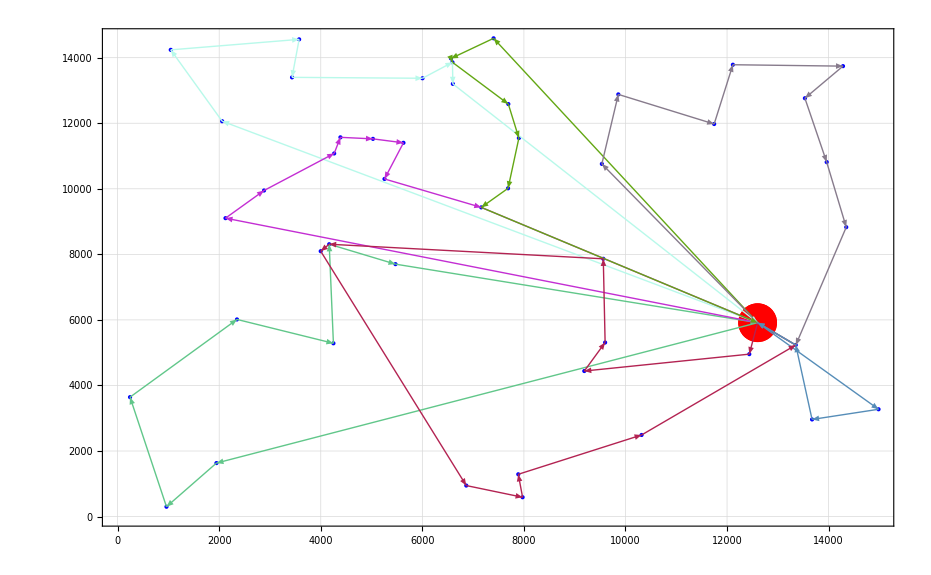

```mathematica
Show[graph,Graphics[arrowlist]]
```

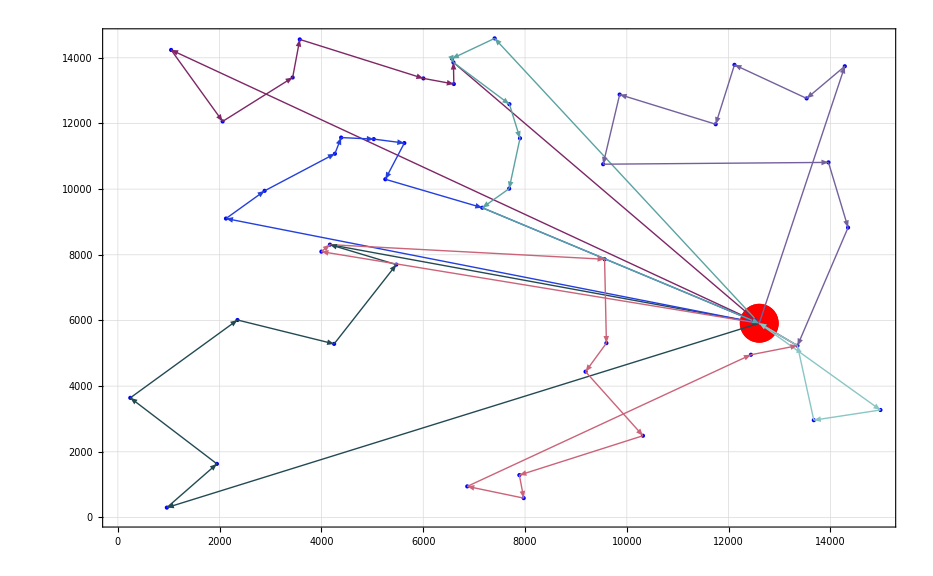

```mathematica
init
```